## Utilities

```mathematica
(* Extract RGB values from Mathematica's "VisibleSpectrum" colour scheme*)
```

```mathematica
vsFunc:=ColorData["VisibleSpectrum"];
vsRGB[c_]:={#[[1]],#[[2]],#[[3]]} &[vsFunc[c]];

(* Map the Reals onto the internal [380, 750] ie. the domain of vsRGB *)
domainMap[eig_,scaling_]:=565+(ArcTan[eig*scaling]/Pi)*370;

(* Given a table of list of pairs {eigenvalue, multiplicity}, re-map the eigenvalues to the interval [380, 750] using domainMap, and define an association scheme between the mapped value and multiplicity*)
remappedSpectrum[spec_,scaling_]:=Association[Table[domainMap[eigMult[[1]],scaling]->eigMult[[2]],{eigMult,spec}]];

(* Scale RGB values based on the multiplicity, such that eigenvalues with greater multiplicity are percieved as being 'brighter' in the spectrum *)
intensityScale[{r_,g_,b_},mult_,multMax_]:=RGBColor[Min[255,r*#],Min[255,g*#],Min[255,b*#]] &[0.6+(mult/multMax)];

(* Convenience function for finding the largest multiplicity *)
multMax[spec_]:=Max[spec[[All,2]]];

(* Defines a colour map which when plotted gives the 'eigenvalue spectrum' *)
spectralLines[remappedSpec_,multMax_]:=Graphics[{Thickness[0.002],intensityScale[vsRGB[#],remappedSpec[#],multMax],Line[{{#,0},{#,1}}] }&/@Keys[remappedSpec], PlotRange->{{380,750},{0,1}},AspectRatio->0.2,Frame->False];

(* Background for spectral line plot *)
bgColorFunction[c_]:=intensityScale[vsRGB[c],0,1];
bg=DensityPlot[x,{x,380,750},{y,0,1},ColorFunction->bgColorFunction,ColorFunctionScaling->False,AspectRatio->0.2,Frame->False];
```

### Spectral Line Plotting Function

```mathematica
(* Plotting Function *)
spectralLinePlotter[mat_,scaling_]:=Show[bg,spectralLines[remappedSpectrum[#,scaling],multMax[#]],Graphics[{EdgeForm[Thick],Transparent,Rectangle[{380,0},{750,1}]},AspectRatio->0.2]]&[Tally[Eigenvalues[mat]]]
```

## Examples

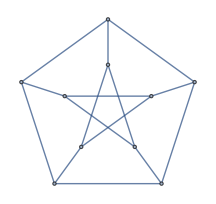

```mathematica
Petersen = PetersenGraph[5,2]
```

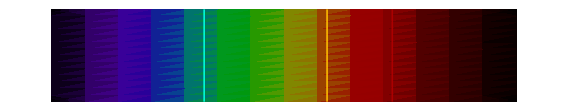

```mathematica
spectralLinePlotter[AdjacencyMatrix[petersen],0.3]
```

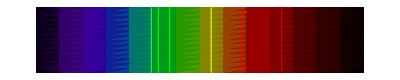
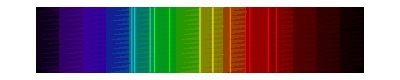
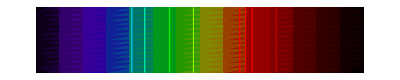
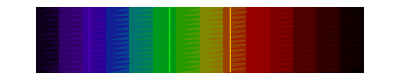
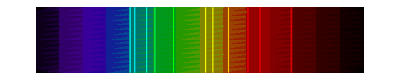
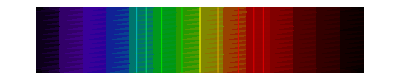
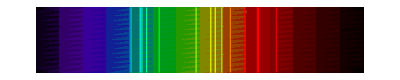
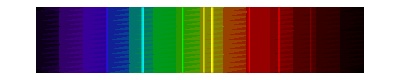
{7,397} | -Graphics-
{Cubic,{14,121}} | -Graphics-
{RegularNonplanarDiameter,{3,3,16,14}} | -Graphics-
{Crown,7} | -Graphics-
{Quartic,{11,165}} | -Graphics-
{Tree,{12,62}} | -Graphics-
RubyGraph | -Graphics-
{Circulant,{19,{1,2,8}}} | -Graphics-
{7,72} | -Graphics-
{Sextic,{11,16}} | -Graphics-

```mathematica
Table[{g,spectralLinePlotter[GraphData[g,"AdjacencyMatrix"], 0.3]},{g, RandomChoice[GraphData[{"Connected"},5;;20],10]}]//Grid
```